# Sistemas de Liénard

Tienen la forma general:

Donde  es una función impar y positiva para  positivas,  es una función par tal que su integral sea negativa para , cero en  y positiva para .

## Ejemplo

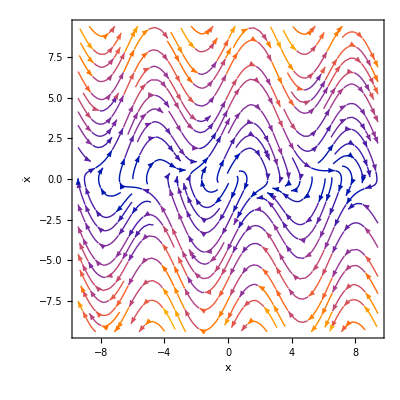

```mathematica
sp1=StreamPlot[{y,2*Cos[x]*y-Tanh[x]},{x,-3*Pi,3*Pi},{y,-3*Pi,3*Pi},FrameLabel->{x,OverDot[x]}]
```

```mathematica
sol1=NDSolve[{x''[t]-2*Cos[x[t]]*x'[t]+Tanh[x[t]]==0,x[0]==0,x'[0]==-0.01},x,{t,0,50}]
```

{{x→InterpolatingFunction[…]}}

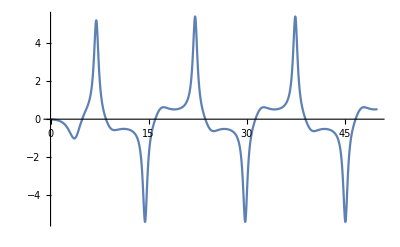

```mathematica
Plot[Evaluate[{x'[t]}/.sol1],{t,0,50},PlotRange->All]
```

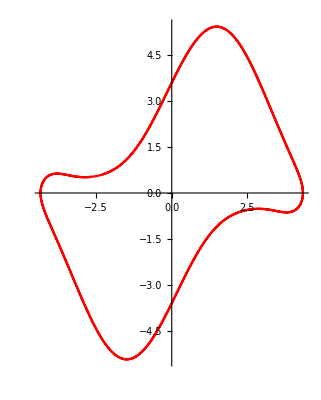

```mathematica
pp1=ParametricPlot[Evaluate[{x[t],x'[t]}/.sol1],{t,20,50},PlotRange->All,PlotStyle->Red]
```

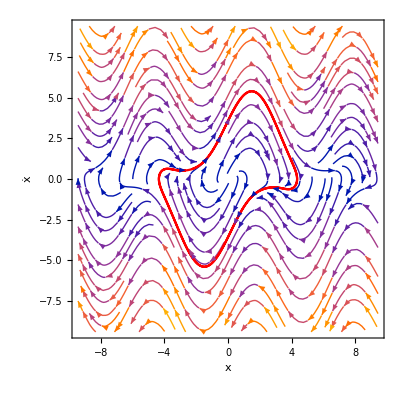

```mathematica
li1=Show[sp1,pp1]
```

## Oscilaciones de relajación

Caracterizaremos las oscilaciones de la ecuación de van der Pol, un caso específico de sistema de Liénard

Primero examinamos el espacio fase:

```mathematica
μ=50;
sol2=NDSolve[{x'[t]==μ*(y[t]-x[t]^3/3+x[t]),y'[t]==-x[t]/μ,x[0]==-1,y[0]==1},{x,y},{t,0,300}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

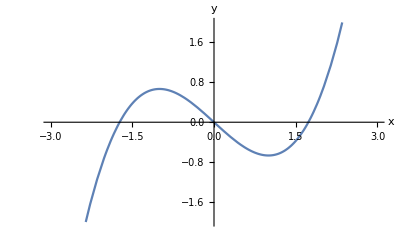

```mathematica
p1=Plot[x^3/3-x,{x,-3,3},PlotRange->{{-3,3},{-2,2}},AxesLabel->{x,y}]
```

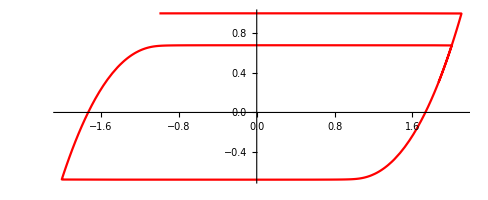

```mathematica
pp2=ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,100},PlotStyle->Red,PlotRange->All]
```

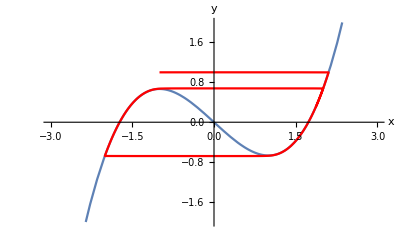

```mathematica
li2=Show[p1,pp2]
```

Y ahora vemos el período:

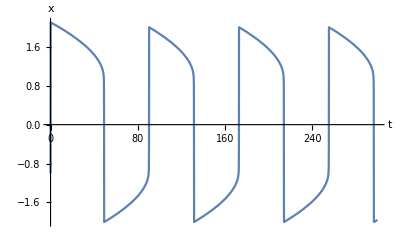

```mathematica
p2=Plot[Evaluate[x[t]/.sol2],{t,0,300},AxesLabel->{t,x}]
```

La teoría aproximada nos dice que el período debe ser

```mathematica
N[μ*(3-2*Log[2])]
```

80.6853

Numéricamente encontramos:

```mathematica
{xsolvdp,ysolvdp}=NDSolveValue[{x'[t]==μ*(y[t]-x[t]^3/3+x[t]),y'[t]==-x[t]/μ,x[0]==-1,y[0]==1},{x,y},{t,0,500}];
N[(t/.FindRoot[xsolvdp[t]==0,{t,170}])-(t/.FindRoot[xsolvdp[t]==0,{t,90}])]
```

82.5083